## Programming Project #3 -Nrepesh Joshi

## a.

### A satellite of mass m moves in the gravitational field of a space station of mass 2 m.The space station maintains a fixed position at the origin.The satellite approaches from the negative x direction along the line y = R, where R is constant, and its velocity is v0 when it is very far from the space station.Assume the magnitude of the gravitational attraction between the satellite and the space station is given by F = k/r^2, where k = 2 m (v0^2) R a.Write a Mathematica program to draw the orbital path of the satellite, by solving the differential equations of the satellite' s motion using Euler' s method.Take m = 1, R = 1, and v0 = 1.

```mathematica
m=1;
R=1;
v0=1;
θ0=π;
rx0=-1;
rx=rx0;
ry=R;
vx=-v0 Cos[θ0];
vy=v0 Sin[θ0];
k=2m v0^2 R;
t=0;
dt=.01;
count=0;
```

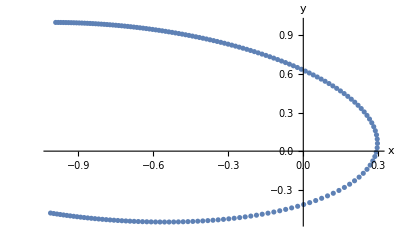

```mathematica
trajectoryList={};
reached=False;
While[!reached,
r=√(rx^2+ry^2);
ax=-k/r rx/(rx^2+ry^2);
ay=-k/r ry/(rx^2+ry^2);
vx+=ax dt;
vy+=ay dt;
rx+=vx dt;
ry+=vy dt;
trajectoryList=Append[trajectoryList,{rx,ry}];
count++;
If[rx≤ rx0||count==10000,reached=True];
]
ListPlot[trajectoryList,AxesLabel->{"x","y"}]
```

### b.From your program, find the distance rmin of closest approach to the space station, and also find the limiting direction of the outgoing satellite, expressed as an angle measured counterclockwise from the positive x - axis.

```mathematica
m=1;
R=1;
v0=1;
θ0=π;
rx0=-1;
rx=rx0;
ry=R;
vx=-v0 Cos[θ0];
vy=v0 Sin[θ0];
k=2m v0^2 R;
t=0;
dt=.01;
count=0;
```

```mathematica
trajectoryList={};
reached=False;
While[!reached,
r=√(rx^2+ry^2);
ax=-k/r rx/(rx^2+ry^2);
ay=-k/r ry/(rx^2+ry^2);
vx+=ax dt;
vy+=ay dt;
rx+=vx dt;
ry+=vy dt;
trajectoryList=Append[trajectoryList,{rx,ry}];
count++;
If[rx≤ rx0||count==10000,reached=True];
If[r<rmin,
rmin=r];
angle = ArcTan[ry/rx];
finalAngel= π+angle;
]
Print["rmin is  ",rmin]
Print["angel is " ,finalAngel]
```

rmin is  rmin

angel is 3.58584

### c.Compare your approximate answer for rmin in part (b) to the answer you find from an exact calculation, starting with the energy conservation equation E = 1/2 m (rdot^2) + Ueff (r) and solving for r at the turning point (when rdot = 0)

```mathematica
Ene=1/2 m v0^2;
l=m v0 R;
(*Solving E=1/2 m (rdot^2)+Ueff (r) When potential = 0*) 
r=-k/(2Ene)+√((k/(2 Ene))^2+l^2/(2 m Ene))//N
```

0.236068